# Report Project 2

Course code: IX1500
Date: 2018-10-01

Maher Jabbar, maherj@kth.se
Simon Lagerqvist,

Task : (1)  RSA cipher

## Summery

### Task

Professor Alice is sending a message to the student Bob according to the procedure in section Section.Subsection.4. You are supposed to crack the message. When translating to ASCII, you can assume the base 256.

```mathematica
nBob=126456119090476383371855906671054993650778797793018127;
eBob=7937;
```

```mathematica
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
```

● The numbers in the list seems to be of the same size. Why?

### Result

1. The plain text is:
“Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.”

2. The numbers in the list must be same size (and can not be less than nBob) otherwise the information would be lost while proceeding with Mod operation.

## RSA cipher

### The Model The RSA decryption process that will be used in code section are in the following steps: 1. Extract the two prime numbers pBob and qBob from Bobs public key (nBob). 2. Finding the private key for Bob (dBob) by finding the modular inverse of eBob mod (p-1)(q-1) 3. Recovering plain text from cipher text by computing: cipher^dBob mod (nBob)

## Code

```mathematica
ClearAll["`*"]
nBob=126456119090476383371855906671054993650778797793018127; (* public key *)
eBob=7937; (* encryption key *)
base = 256; (* base is 256 *)
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570}; (* cipher text *)
(* extraction p and q from nBob *)
pAndq=FactorInteger[nBob]; 
pBob=pAndq[[1,1]];
qBob=pAndq[[2,1]];
(* finding decryption (private)key dBob *)
ϕBob=(pBob-1)(qBob-1);
dBob=PowerMod[eBob, -1, ϕBob];
(* cracking the cipher message *)
plaincode=PowerMod[cipher, dBob, nBob];
(* buffer to hold message *)
plaintext[0]:={}
plaintext[num_]:=Prepend[plaintext[Quotient[num, base]], Mod[num,base]]
(* reconstruct the original message from ascii codes *)
FromCharacterCode[Join@@plaintext/@plaincode]
```

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.

Task : (2)  RSA decryption analysis

## Summery

### Task

Write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the English text “ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.” for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits

● Motivate your selected mathematical model!

### Result

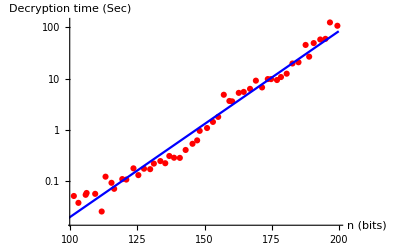
1. The time for cracking the cipher of the English text “ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.” was 0.0876087 seconds

2. The decryption time vs key sizes (100-200 bits) from the output of code section (where the red points represents the normal data and the blue line represents the fitted data) is:
 
                       -Graphics- 
                       
 3. The prediction time (years) for different n (bits) is: 
  
                   n (bits) | Decryption Time (years)
1024 | 1.45098×10^24
2048 | 1.32113×10^61
4096 | 1.09527×10^135

## RSA decryption analysis

### The Model The comments in the code section provides information regarding the mathematical model that is used in encryption and decryption processes.

## Code

```mathematica
ClearAll["`*"]

(* Generate 2 random prime numbers (50-60) bits *)
p=NextPrime[RandomInteger[{2^50,2^60 }]]
q = NextPrime[RandomInteger[{2^50,2^60}]]
```

1140034711220253077

407911063164465181

```mathematica
(* Finding public and private keys (100 bits)*)
n = p *q 
ϕ=(p-1)(q-1)
```

465032771098247474895212504174611937

465032771098247473347266729789893680

```mathematica
(* Generate random encryption key *)
RandomSeed[];
While[GCD[e=RandomInteger[{10^20,10^30}],ϕ]≠1];
e
```

246887640620478078740700934997

```mathematica
(* Evaluate dncryption key *)
d=PowerMod[e,-1,ϕ]
```

117879920915019989858578074078996173

```mathematica
(* the given plain text *)
mes="ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.";
```

```mathematica
(* Breaking message into parts (each part is 8 bytes) *)
mesLen=Range[StringLength[mes]]-1;
base=256;
buffer[0]:={}
buffer[num_]:=Prepend[buffer[Quotient[num, base^8]], Mod[num, base^8]]
mesParts=buffer[ToCharacterCode[mes]. (base^mesLen)]
```

{5713190297443521601,5644453189917089870,2315207907610023497,4919987194625546562,5208212111155744079,3336117587843424340}

```mathematica
(*** Encryption process ***)
cipher=PowerMod[mesParts,e,n]
```

{367506590861571440673576877361672089,201150355700743870243854501960849767,24167944698878847510754999550831335,227587766067852566367591399428658979,254037900587904333909734513203968462,197084203568602584852089262584532786}

```mathematica
(*** Decryption Method ***)

(* when ϕ is known *)
RSAonePart[cipher_, n_, e_, ϕ_]:=
Module[{code, str},
code={};
str=PowerMod[cipher,PowerMod[e,-1,ϕ],n];
While[str≠0,
AppendTo[code,Mod[str,base]];
str=Quotient[str,base]
];
code;
FromCharacterCode[code]
]

(* when ϕ is unknown) *)
RSAcrack[cipher_,n_,e_]:=Module[{str, fact,ϕ, code}, 
fact = FactorInteger[n];
ϕ=Times@@(fact[[All,1]]-1);
code={};
StringJoin@@(RSAonePart[#, n, e, ϕ]&/@cipher)
]
```

```mathematica
(*** Decryption Process ***)
AbsoluteTiming[RSAcrack[cipher,n,e]]
```

{0.0876087,ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.}

```mathematica
(*** different sizes of public key (100-200 bits) ***)
time={}; nBits ={};
RandomSeed[];
For[i=0,i<50,i++,
p=NextPrime[RandomInteger[{2^(50+i),2^(51+i)}]]; 
q=NextPrime[RandomInteger[{2^(50+i),2^(51+i)}]];
n =p *q; 
ϕ=(p-1)(q-1);
e=0;
While[GCD[e=RandomInteger[{10^20,10^30}],ϕ]≠1];
cipher=PowerMod[mesParts,e,n];
AppendTo[time,AbsoluteTiming[RSAcrack[cipher,n,e]][[1]]];
AppendTo[nBits,  N[Log[2,n]]];
]
```

```mathematica
(*** Plotting time vs. key sizes ***)
fitData=FindFit[Transpose [{nBits, Log[time]}],slope* x+const,{slope,const},x];
y[x_]=Exp[slope* x+const]/.fitData
listPlot=ListLogPlot[Transpose [{nBits, time}],AxesLabel->{"n (bits)","Decryption time (Sec)"},PlotStyle->Red];
fitPlot=LogPlot[y[x],{x,50,200},AxesLabel->{"n (bits)","Decryption time (Sec)"},PlotStyle->Blue];
Show[listPlot,fitPlot]
```

ⅇ^(-12.201+0.0831073 x)

-Graphics-

```mathematica
(*** Calculating prediction time table ***)
t=60*60*24*365; (* seconds to year *)
list={{1024,y[1024]/t},{2048,y[2048]/t},{4096,y[4096]/t}};
TableForm[list,TableHeadings -> {None,{"n (bits)","Decryption Time (years)"}},TableAlignments -> Center]
```

n (bits) | Decryption Time (years)
1024 | 1.45098×10^24
2048 | 1.32113×10^61
4096 | 1.09527×10^135